Тема 6. Функції і графіки.

Завдання 1. Побудова графіка функції по точках.

Використовуючи систему «Mathematica», побудувати графік функції y (x) та таблицю її значень. Інтервал для незалежної змінної підібрати самостійно. Побудувати графік ламаної, використовуючи таблицю значень. На одному рисунку зобразити графік функції та ламаної.

```mathematica
Remove[x,y]
```

```mathematica
y[x_]=-12*(6*(x-1)^2)^(1/3)/(x^2+2*x+9);
```

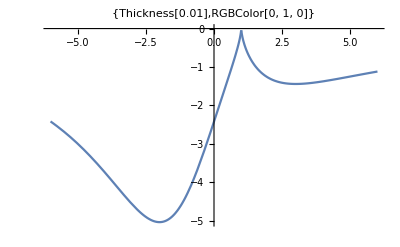

```mathematica
p1=Plot[y[x],{x,−6,6},PlotLabel->{Thickness[0.01],Green}]
```

```mathematica
pt = Table[{x,y[x]},{x,-6,6,1}]
```

{{-6,-4/11 6^(1/3) 7^(2/3)},{-5,-3},{-4,-12/17 5^(2/3) 6^(1/3)},{-3,-2 2^(2/3) 3^(1/3)},{-2,-4 2^(1/3)},{-1,-3 3^(1/3)},{0,-(4 2^(1/3))/3^(2/3)},{1,0},{2,-(12 6^(1/3))/17},{3,-3^(1/3)},{4,-(12 2^(1/3))/11},{5,-6/11 2^(2/3) 3^(1/3)},{6,-4/19 5^(2/3) 6^(1/3)}}

```mathematica
N[pt]//TableForm
```

-6. | -2.41796
-5. | -3.
-4. | -3.75056
-3. | -4.57886
-2. | -5.03968
-1. | -4.32675
0. | -2.42283
1. | 0.
2. | -1.28267
3. | -1.44225
4. | -1.37446
5. | -1.24878
6. | -1.11859

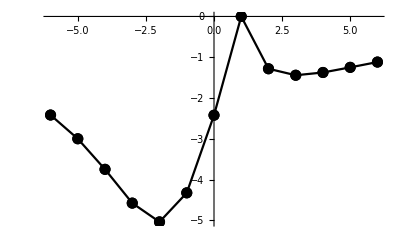

```mathematica
p2 = ListPlot[pt, Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Black}]
```

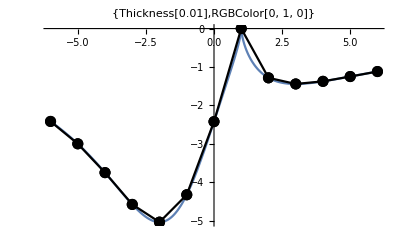

```mathematica
Show[p1,p2]
```

Завдання 2. Побудова графіка полінома.

Використовуючи систему «Mathematica», побудувати графік полінома y(x) . Інтервал для незалежної змінної підібрати самостійно.

```mathematica
Remove[x,y]
```

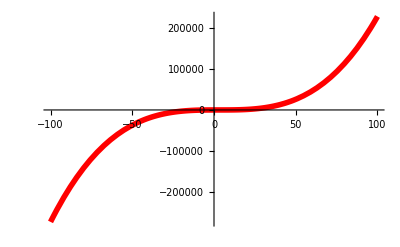

```mathematica
y[x_]=(x^3-9*x^2)/4+6*x-9;
Plot[y[x],{x,-100,100},PlotStyle->{Thickness[0.01],Red}]
```

Завдання 3. Побудова графіка явно заданої функції.

Використовуючи систему «Mathematica», побудувати графік функції y (x). Інтервал незалежної змінної на графіку підібрати самостійно.

```mathematica
Remove[x,y]
```

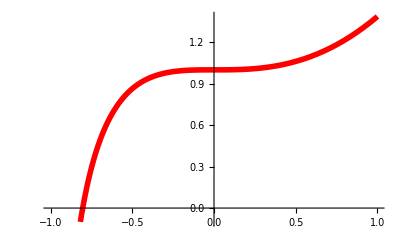

```mathematica
y[x_]=x^2-2*x+2*Log[x+1]+1;
Plot[y[x],{x,-1,1},PlotStyle->{Thickness[0.01],Red}]
```

Завдання 4. Побудова графіка параметричної функції по точках.

Використовуючи систему «Mathematica», побудувати графік функції, яка задана параметрично. Побудувати таблицю координат вузлів ламаної на інтервалі [0,2π]. Побудувати її графік, використовуючи цю таблицю значень. На одному рисунку зобразити графік функції та ламаної.

```mathematica
Remove[x,y,t]
```

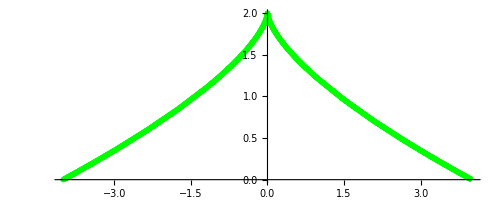

```mathematica
x[t_]=4*Cos[t]^3;
y[t_]=2*Sin[t]^2;
p1 = ParametricPlot[{x[t],y[t]},{t,0,2π},AspectRatio->Automatic, PlotStyle->{Thickness[0.01],Green}]
```

```mathematica
pt=Table[{x[t],y[t]},{t,0,2π, π/4}]
```

{{4,0},{√2,1},{0,2},{-√2,1},{-4,0},{-√2,1},{0,2},{√2,1},{4,0}}

```mathematica
N[pt]//TableForm
```

4. | 0.
1.41421 | 1.
0. | 2.
-1.41421 | 1.
-4. | 0.
-1.41421 | 1.
0. | 2.
1.41421 | 1.
4. | 0.

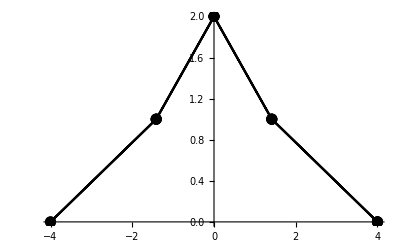

```mathematica
p2=ListPlot[pt,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02], Black}]
```

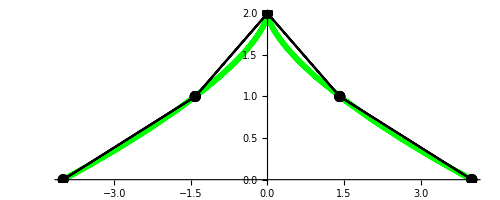

```mathematica
Show[p1,p2]
```

Завдання 5. Побудова графіка функції, яка задана параметрично.

Використовуючи систему «Mathematica», побудувати графік функції, яка задана параметрично.

```mathematica
Remove[x,y,t]
```

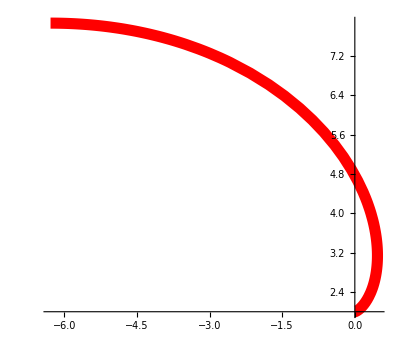

```mathematica
x[t_]=(t^2-2)*Sin[t]+2*t*Cos[t];
y[t_]=(2-t^2)*Cos[t]+2*t*Sin[t];
p1 = ParametricPlot[{x[t],y[t]},{t,0,π},PlotStyle->{Thickness[0.02],Red}]
```

Завдання 6. Побудова графіка функції, яка задана неявно.

Використовуючи систему «Mathematica», побудувати графік функції, яка задана неявно. Діапазони зміни незалежних змінних підібрати самостійно.

```mathematica
Remove[x,y,F]
```

```mathematica
F[x_,y_]=-2*x^2-2*y^2+2*x*y-6*x+6*y+3;
```

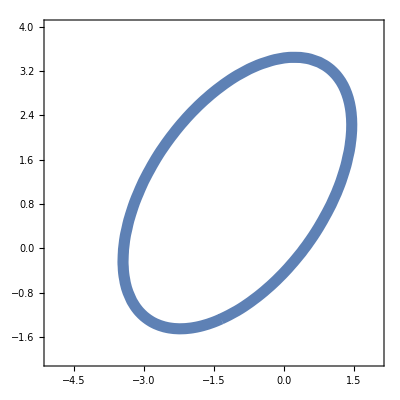

```mathematica
ContourPlot[F[x,y]==0,{x,-5,2},{y, -2,4},ContourStyle->{Thickness[0.02]}]
```